# Math 223: Homework 2

Ali Heydari

Feb. 4th, 2021

## Problem 1

Classify the points at 0 and ∞ of the following differential equations:

(a) x^7 y^(4) = y'

In order to check for singularity points (and classify them), we will rewrite the equation in standard form: 
x^7 y^(4) - y' = 0
= y^(4)  - y'/x^7 = 0
To check for singularity at 0, we can study the behavior as x → 0, which is clearly not finite (therefore a singular point). Now to classify the singular point, we must look at if each term 
(x-x_0)^n p_0(x), (x-x_0)^(n-1)p_1(x), ⋯ ,(x-x_0)p_(n-1)(x) are analytic in a neighborhood of x_0.

```mathematica
n = 7;
x0 = 0;
p1[x_]:=1/(x^7);
p1[x]
(*Series[(x-x0)^(n-1) * p1, {x,x0,10}]*)
```

1/x^7

```mathematica
Series[(x-x0)^(n-1) * p1[x], {x,x0,10}]
```

1/x+O[x]^11

which is not analytic at x = 0, therefore resulting in an essential singularity. That makes sense since we have a pole of order 7 for  p(x)  = 1/x^7, but the differential equation is of order 4.
To check the same thing for x → ∞ , we have to use an inversion mapping (i.e. x = 1/t), and then checking the analyticity of f(t). Since we will be having the same derivatives, we can calculate 
these values, and keep using them. Taking  f = y(1/x) = y(t)

```mathematica
dt = D[y[1/x], {x,1}]
```

-y'[1/x]/x^2

```mathematica
dt2 =  D[y[1/x], {x,2}]
```

(2 y'[1/x])/x^3+y''[1/x]/x^4

```mathematica
dt3 =  D[y[1/x], {x,3}]
```

-(6 y'[1/x])/x^4-(6 y''[1/x])/x^5-(y^(3)[1/x])/x^6

```mathematica
dt4 = D[y[1/x], {x,4}]
```

(24 y'[1/x])/x^5+(36 y''[1/x])/x^6+(12 y^(3)[1/x])/x^7+(y^(4)[1/x])/x^8

So rewriting these values in terms of t, we have:

d/dx= -t^2 d/dt

d^2/dx^2= t^4 d^2/dt^2 + 2 t^3 d/dt

d^3/dx= t^6 d^3/dt^3 -6 t^5 d^2/dt^2 - 6 t^4 d/dt

d^4/dx= t^8 d^4/dt^4 +12 t^7 d^3/dt^3 +36 t^6 d^2/dt^2 + 24 t^5 d/dt

So now to check for the behavior at x_0=∞ , we use the inversion mapping:

y^(4)  - y'/x^7 = 0 →  t^8 y^(4) +12 t^7 y^(3) +36 t^6 y'' + 24 t^5 y' + t^7 y' = 0
= y^(4) +12/t  y^(3) +36/t^2 y'' + 24/t^8 y' + y' 1/t = y^(4) +12/t  y^(3) +36/t^2 y'' + (24/t^3 +1/t)y' =0

Given the expression above, we can quickly asses that the singularity at infinity will be a regular point, 
since the order of each derivative is higher than the pole. But to concretely check for this, we can check 
to see if the coefficients are analytic or not. Let us start by p_1(t) first:

```mathematica
n = 7;
t0 = 0;
p1[t_]:= (24/t^3 +1/t);
Series[(t-t0)^(n-1) * p1[t], {t,t0,15}]
```

24 t^3+t^5+O[t]^16

so the first set of coefficient is analytical. Now checking for the rest:

```mathematica
p2[t_]:= (36/t^3);
Series[(t-t0)^(n-2) * p2[t], {t,t0,15}]
```

36 t^2+O[t]^16

```mathematica
p3[t_]:= (12/t);
Series[(t-t0)^(n-3) * p3[t], {t,t0,15}]
```

12 t^3+O[t]^16

which are all analytic, therefore we have a regular singularity at the point  x →x_0, where x_0= ∞ .

(b) x^3 y^(3) = y

Following our approach in the part (a), we have:

```mathematica
y^(3)  - y/x^3 = 0
```

so we have p_0(x) = 1/x^3, which has a singularity at x_0 = 0. Now, to classify the type of singularity at x_0=0, we look at the analyticity of (x-x_0)^n p_0(x) :

```mathematica
n = 3;
x0 = 0;
p0[x_] = 1/(x^3);
```

```mathematica
Series[(x-0)^n * p0[x], {x,x0,15}]
```

1

which is pretty analytic if you ask me. So the singularity at x_0=0 for p_0(x) is a regular singular point (poll of order 3). Now to check for x_0= ∞, 
we use the derivates of the transformation that we found in (a), which gives us:

t^6 y^(3)-6 t^5 y'' - 6 t^4 y' + t^3 y = 0
= y^(3) - 6/t y'' - 6/t^2 y' + 1/t^3 y = 0

here we can see that the pole with the highest degree (p_0(t)) has the exact same degree as the differential equation (order 3), which means 
that we will have a regular singular point. But to confirm this:

```mathematica
p0[t_] = 1/t^3;
 p1[t_] = -6/t^2;
 p2[t_] = -6/t;
t0 = 0;
```

```mathematica
Series[(t-t0)^n*p0[t],{t,t0,10}]
```

1

```mathematica
Series[(t-t0)^(n-1)*p1[t],{t,t0,10}]
```

-6

```mathematica
Series[(t-t0)*p2[t],{t,t0,10}]
```

-6

which are all analytic at t_0=0, implying that we have a regular singular point at x_0= ∞ as well.

(c)  y^(3) = x^3 y

writing the equation in the normal form gives us y^(3) - x^3 y = 0, which does not have any singularities at the point x_0 = 0, so we have an ordinary point.
To check for the point x_0= ∞, we can rewrite the equation in the terms of the inversion mapping as follows: 
t^6 y^(3)-6 t^5 y'' - 6 t^4 y' + 1/t^3 y = 0
= y^(3) - 6/t y'' - 6/t^2 y' + 1/t^9 y = 0
looking at the order of the pole for p_0(x) (9) and the order of the ODE (3), we can see that we will have an irregular singularity. To check for the analyticity:

```mathematica
n = 3;
t0 = 0;
p0[t_] = 1/t^9;
Series[(t-t0)^n*p0[t],{t,t0,10}]
```

1/t^6+O[t]^11

which is clearly not analytic at the point t_0= 0. Therefore we have an irregular singular point at x_0 = ∞.

(d) x^2 y^(2) = e^(1/x) y

As usual, let us write this in the normal form:
y^(2) - e^(1/x)/x^2 y  = 0
and to check for possible singularities at the x_0 = 0 and x_0=∞ :

```mathematica
n = 2;
x0 = 0;
t0 = 0;
px0 = (E^(1/x))/(x^2);
```

```mathematica
Series[(x-x0)^n*px0,{x,x0,10}]
```

```mathematica
ⅇ^(1/x+O[x]^12)
```

which has is not analytic at x_0 = 0, therefore we have an irregular singularity.
Now to check for x_0= ∞, we do the usual inverted mapping of t = 1/x: 
t^4/t^2 y'' +2 t^3/t^2 y' - e^t y = y’’ + 2/ty’ - e^t/t^2 y = 0

which we can tell will result in regular singular points, since the order of the ODE matches the order of the highest degree pole. 
To check for analyticity:

```mathematica
n = 2;
t0 = 0;
p0[t_] = -e^t/t^2;
 p1[t_] = 2/t;
```

```mathematica
Series[(t-t0)^n*p0[t],{t,t0,10}]
```

-1-Log[e] t-1/2 Log[e]^2 t^2-1/6 Log[e]^3 t^3-1/24 Log[e]^4 t^4-1/120 Log[e]^5 t^5-1/720 Log[e]^6 t^6-(Log[e]^7 t^7)/5040-(Log[e]^8 t^8)/40320-(Log[e]^9 t^9)/362880-(Log[e]^10 t^10)/3628800+O[t]^11

```mathematica
Series[(t-t0)^(n-1)*p1[t],{t,t0,10}]
```

2

which are all analytic as we suspected, therefore we have a regular singularity at x_0= ∞.

(e) tan(x) y' = y

writing this in the standard form, we get y'  - y/(tan(x))= 0 . We know we have a singularity for p_0(x), but it should be a regular singularity (do to the behavior of tan(x). 
To check the analyticity:

```mathematica
n=1;
x0 = 0;
p0[x_]=1/Tan[x];
Series[(x-x0)^n*p0[x],{x,x0,10}]
```

```mathematica
1-x^2/3-x^4/45-(2 x^6)/945-x^8/4725-(2 x^10)/93555+O[x]^11
```

which is very analytic! so we have a regular singularity at x_0 = 0. For x_0= ∞, as usual we use x=1/t , which yields:
-t^2y'  - y/(tan(x))= y' + y/(t^2 tan(x))=0.

Now the addition of t^2 to the denominator for a first order ODE is problematic, so we expect an irregular singular point. To check this:

```mathematica
n=1;
t0 = 0;
p0[t_]=1/(t^2 Tan[1/t]);
Series[(t-t0)^n*p0[t],{t,t0,10}]
```

Cot[1/t+O[t]^11] (1/t+O[t]^11)

which is not analytic at t = 0, therefore we have an irregular singularity at x_0= ∞, as expected.

(f) y^(2) = (log(x))y

so we have  y'' - (log(x))y = 0, with log(x) having a singularity at 0. We can immediately suspect to have an irregular singular point do to the logarithm.
Studying this point, we find that:

```mathematica
n = 1;
x0 = 0;
p0[x_] = Log[x];
Series[(x-x0)^n*p0[x],{x,x0,10}]
```

```mathematica
Log[x] x+O[x]^11
```

which is not analytic at x_0 = 0, therefore having an irregular singular point. Again due to the logarithm, we can expect the same thing 
at x_0=∞, but solving for it we have:

t^4 y'' +2 t^3 y' - log(x) y = y’’ + 2/ty’ - (log(x))/t^4 y = 0

```mathematica
n=2;
t0 = 0;
p0[t_]=Log[1/t]/t^4;
Series[(t-t0)^n*p0[t],{t,t0,10}]
```

Log[1/t]/t^2+O[t]^11

which is not analytic, therefore resulting in an irregular singular point at x_0 = ∞ .

## Problem 2

For the initial value problem:
	(x- 1)(x-2)y''+ (4x - 6) y' + 2y = 0,             
                                           y(0) = 0 ,
                                           y'(0) = 1
where might one expect the series solution about x = 0 to converge? Compute the Taylor expansion about x = 0 of the solution and determine the radius of convergence.

```mathematica
Mathematica Solution
```

## Problem 3

For the following differential equations, where would you expect the series solution about x = 0 to converge? Find series expansions of all the solutions to the following differential equations about x=0. Try to sum in closed form any infinite series that appear.

By Fuch’s theorem, if we have a regular singular point, then the series solution will have a radius of convergence at least to the nearest singularity. So in the following problems, we will do:
1) Ensure that we have regular singularity at x_0 = 0
2) Use Mathematica to solve each problem, and then expand each solution about 0

*Note: I was not too sure if I had to actually solve the problems by hand, and when I asked no one had solved the problems by hand. But just in case if we were supposed to, I wrote up the solution to part (c) to show how it can be done by hand.

(a) x y'' + y= 0

To find solve this problem, we can use DSolve to find the close form of the solution.

```mathematica
solution  = DSolve[x*y''[x] + y[x] == 0, y[x], x]
```

{{y[x]→√x BesselJ[1,2 √x] C[1]+2 ⅈ √x BesselY[1,2 √x] C[2]}}

now that we have found the solutions to be Bassel function, we know that they are of the form:

y_1 = ∑_(m=1)^∞ i^2


expand them around x=0 and look at the radius of convergence:

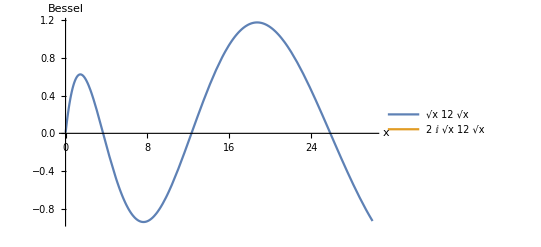

```mathematica
plot=Plot[{√x BesselJ[1,2 √x],2 ⅈ √x BesselY[1,2 √x]},{x,0.01,30},AxesLabel->{x,Bessel},PlotStyle->{Thick},PlotLegends->"Expressions"]
(*left=Graphics[Text[Style["\!\*SubscriptBox[\(J, 0]\)(x)"],{1.5,0.95}]];
center=Graphics[Text[Style["\!\*SubscriptBox[\(J, 1]\)(x)"],{2.2,0.65}]];
right=Graphics[Text[Style["\!\*SubscriptBox[\(J, 2]\)(x)"],{4.0,0.55}]];
Show[plot,left,center,right]*)
```

```mathematica
ComplexPlot[2 ⅈ √x BesselY[1,2 √x],{x,-2-2 I,2+2 I},PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
ComplexPlot[(z^2+1)/(z^2-1),{z,-2-2 I,2+2 I}]
```

```mathematica
firstSol = √x BesselJ[1,2 √x] C[1];
secondSol = 2 ⅈ √x BesselY[1,2 √x] C[2];
firstSeries = Series[firstSol, {x,0,10}]
secondSeries = Series[secondSol, {x,0,10}]
```

C[1] x-(C[1] x^2)/2+(C[1] x^3)/12-(C[1] x^4)/144+(C[1] x^5)/2880-(C[1] x^6)/86400+(C[1] x^7)/3628800-(C[1] x^8)/203212800+(C[1] x^9)/14631321600-(C[1] x^10)/1316818944000+O[x]^11

-(2 ⅈ C[2])/π+(2 ⅈ C[2] (-1+2 EulerGamma+Log[x]) x)/π-(ⅈ C[2] (-5+4 EulerGamma+2 Log[x]) x^2)/(2 π)+(ⅈ C[2] (-10+6 EulerGamma+3 Log[x]) x^3)/(18 π)-(ⅈ C[2] (-47+24 EulerGamma+12 Log[x]) x^4)/(864 π)+(ⅈ C[2] (-131+60 EulerGamma+30 Log[x]) x^5)/(43200 π)-(ⅈ C[2] (-71+30 EulerGamma+15 Log[x]) x^6)/(648000 π)+(ⅈ C[2] (-353+140 EulerGamma+70 Log[x]) x^7)/(127008000 π)-(ⅈ C[2] (-1487+560 EulerGamma+280 Log[x]) x^8)/(28449792000 π)+(ⅈ C[2] (-6989+2520 EulerGamma+1260 Log[x]) x^9)/(9217732608000 π)-(ⅈ C[2] (-1451+504 EulerGamma+252 Log[x]) x^10)/(165919186944000 π)+O[x]^(21/2)

{{Series[y[x]→√x BesselJ[1,2 √x] C[1]+2 ⅈ √x BesselY[1,2 √x] C[2],{x,0,10}]}}

(b)  y''  + (e^x- 1)y= 0

```mathematica
solution  = DSolve[y''[x] + (E^x - 1)* y[x] == 0, y[x], x]
```

{{y[x]→2 BesselJ[2,2 √(ⅇ^x)] C[1]+2 BesselY[2,2 √(ⅇ^x)] C[2]}}

```mathematica
Series[BesselJ[1,2 √x],{x,0,10}]
```

√x-x^(3/2)/2+x^(5/2)/12-x^(7/2)/144+x^(9/2)/2880-x^(11/2)/86400+x^(13/2)/3628800-x^(15/2)/203212800+x^(17/2)/14631321600-x^(19/2)/1316818944000+O[x]^(21/2)

(c)  (sin(x))y''  - 2(cos(x))y' -  (sin (x))y= 0

```mathematica
Mathematica Solution
```